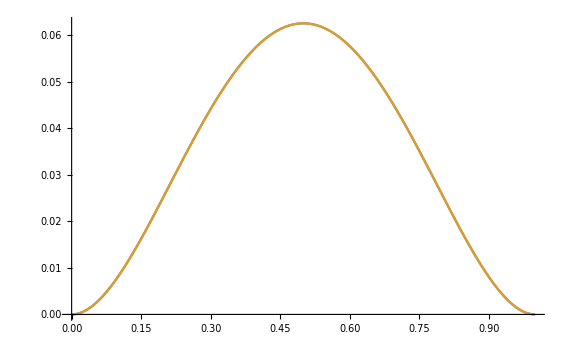

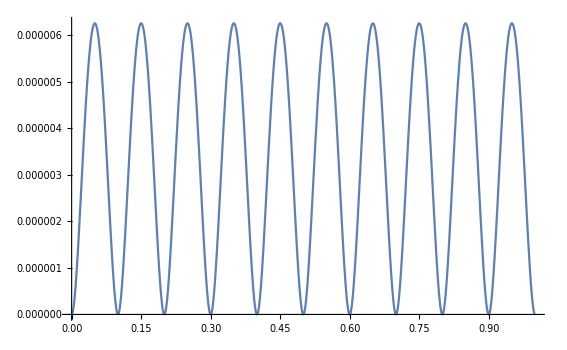

```mathematica
(* Проект по Числен Анализ 
 Минчо Стефанов Паскалев, КН, гр.2, ФН № 81568 *)

n=10;

(*функцията,която ще бъде интерполирана от търсения естествен кубичен сплайн*)
f[t_]:= t^2(t-1)^2;
(*генерираме интерполационните възли*)
Do[x[k]=k/n,{k,0,n}];

Δ=1/n; (* Subscript[x, i+1]-Subscript[x, i] ∀i ∈ {0,...,n-1}*)

(* Решаваме система по метода на прогонката *) 

(* Коефициентите имаме от теорията получени чрез намиране на разделени разлики и после приравняване на p''(Subscript[x, i]) = p''(Subscript[x, i+1]). Тъй като те зависят от Subscript[x, i+1] - Subscript[x, i] = Δ, но Δ = 1/n за всяко i ∈ {1,...,n} имаме следното: *) 
Subscript[a, i]=1/Δ; 
Subscript[b, i]= 4/Δ ; 
Subscript[c, i]=1/Δ;
Do[rhs[k]=3*(f[x[k]]-f[x[k-1]])/Δ^2+3*(f[x[k+1]]-f[x[k]])/Δ^2,{k,1,n-1}]; (* rhs == Right-hand side *)


(* прав ход на прогонката - пресмятаме Subscript[α, k] и Subscript[β, k]. *)
α[1]=-Subscript[c, i]/Subscript[b, i]; 
β[1]=rhs[1]/Subscript[b, i];
Do[α[k]=-Subscript[c, i]/(Subscript[a, i]*α[k-1]+Subscript[b, i]),{k,2,n-1}];
Do[β[k]=(rhs[k]-Subscript[a, i]*β[k-1])/(Subscript[a, i]*α[k-1]+Subscript[b, i]),{k,2,n-1}];

(* Следните са поради факта че правим пълна кубична интерполация, а не се намираме в случая на естествен кубичен сплайн *)
s[0] = f'[x[0]];
s[n] = f'[x[n]];

(*обратен ход на прогонката*)
s[n-1]=β[n-1]; (* този ред идва по естествен начин от метода на прогонката *)
Do[s[k]=α[k]*s[k+1]+β[k],{k,n-2,1,-1}];

(* общ вид на полиномите интерполиращи f(t) във всеки подинтервал на [0, 1],определен от два последователни интерполационни възела *)
(* Пресмятаме коефициентите в общия вид за удобство *)
Do[ca[k]=(f[x[k+1]]-f[x[k]])/Δ^2-s[k]/Δ,{k,0,n-1}];
Do[cb[k]=s[k+1]/Δ^2+s[k]/Δ^2+2*(f[x[k]]-f[x[k+1]])/Δ^3,{k,0,n-1}];

Do[p[k,z_]= f[x[k]]+s[k](z-x[k])+ca[k](z-x[k])^2+cb[k](z-x[k])^2(z-x[k+1]) ,{k,0,n-1}];

(* построяване на кубичния сплайн за f(t),като вече имаме интерполиращите полиноми за всеки един интервал (рекурсия)*)
splineRec[i_,t_]:=If[i≤n-1,If[t≥x[i]&&t<x[i+1],p[i,t],splineRec[i+1,t]]];
spline[t_]:=splineRec[0,t];
(*изчертаваме графиките на функцията и сплайн функцията*)
Plot[{f[t],spline[t]}, {t, 0, 1}, PlotPoints->1000, PlotRange->All]
(*изчертаваме графиката на разликата от функцията и сплайн функцията*)
Plot[f[t]-spline[t] , {t, 0, 1}, PlotRange->All]
```